## Random walkers

Here we simulate the one-dimensional random walk we discussed in class on March 30.  Simulate for the following situations.

### Unbiased random walk (l=0.5), one walker (z=1), 100 steps (nmax=100). Does it appear random? (2 pts)

Yes, it appears to be random as the organism seems to be on the left and right of the origin rather randomly.

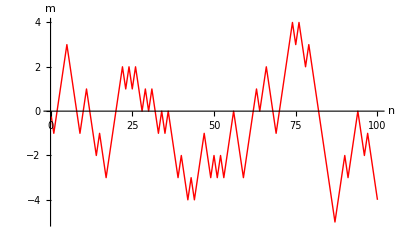

```mathematica
(* parameters *)

nmax=100; (* max steps *)
z=1; (* number of organisms *)

l=0.5; (* prob step left *)

Do[
m[i,0]=0;
,{i,1,z}]

Do[
Do[
If[Random[Real,{0,1}]<l,m[i,n]=m[i,n-1]-1,m[i,n]=m[i,n-1]+1];
,{i,1,z}];
,{n,1,nmax}];

Do[
plot[i]=ListPlot[Table[{n,m[i,n]},{n,0,nmax}],Joined->True,PlotStyle->Hue[i/z],AxesLabel->{"n","m"}];
,{i,1,z}];

Show[Table[plot[i],{i,1,z}]]
```

### Unbiased random walk, ten walkers, 1000 steps. Describe how the dispersion (spread) of the population changes over time. (2 pts)

The population seems to spread more as time increases.  The organisms start out very clustered, but after a while, they separate more and more.

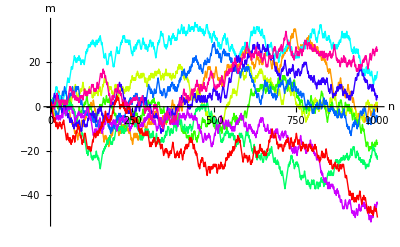

```mathematica
(* parameters *)

nmax=1000; (* max steps *)
z=10; (* number of organisms *)

l=0.5; (* prob step left *)

Do[
m[i,0]=0;
,{i,1,z}]

Do[
Do[
If[Random[Real,{0,1}]<l,m[i,n]=m[i,n-1]-1,m[i,n]=m[i,n-1]+1];
,{i,1,z}];
,{n,1,nmax}];

Do[
plot[i]=ListPlot[Table[{n,m[i,n]},{n,0,nmax}],Joined->True,PlotStyle->Hue[i/z],AxesLabel->{"n","m"}];
,{i,1,z}];

Show[Table[plot[i],{i,1,z}],PlotRange->All]
```

### Unbiased random walk, 100 walkers, 1000 steps. Run and observe the paths of individuals. Then, run the next cell, which plots the density of random walkers in bins and the expected density (solution to diffusion equation) in black. How does the rate of spead of the population change over time? Does the expected density agree with the observed density? (4 pts)

The rate of spread increases over time.  The expected density does agree with the observed density as the density bins look similar to the expected density curves.

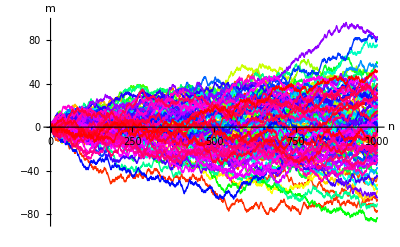

```mathematica
(* parameters *)

nmax=1000; (* max steps *)
z=100; (* number of organisms *)

l=0.5; (* prob step left *)

Do[
m[i,0]=0;
,{i,1,z}]

Do[
Do[
If[Random[Real,{0,1}]<l,m[i,n]=m[i,n-1]-1,m[i,n]=m[i,n-1]+1];
,{i,1,z}];
,{n,1,nmax}];

Do[
plot[i]=ListPlot[Table[{n,m[i,n]},{n,0,nmax}],Joined->True,PlotStyle->Hue[i/z],AxesLabel->{"n","m"}];
,{i,1,z}];

Show[Table[plot[i],{i,1,z}],PlotRange->All]
```

```mathematica
(* the following code will plot the density of organisms (bins) and the expected density, normal distribution solution to diffusion equation (line) *)

If[l==0.5,
mmax=Ceiling[Max[Abs[Max[Flatten[Table[m[i,n],{i,1,z},{n,0,nmax}]]]],Abs[Min[Flatten[Table[m[i,n],{i,1,z},{n,0,nmax}]]]]]/10]*10+5;
mmin=-mmax;,
mmax=Ceiling[Max[Flatten[Table[m[i,n],{i,1,z},{n,0,nmax}]]]/10]*10+5;
mmin=Floor[Min[Flatten[Table[m[i,n],{i,1,z},{n,0,nmax}]]]/10]*10-5;
];

ϵ=0.0001;
d=1/2;

Animate[
hgram=Histogram[Table[m[i,n],{i,1,z}],{10},PlotRange->{{-100,100},All}];
dplot=Plot[10*z/(2*Sqrt[π*d*(n+ϵ)])*E^(-(x-(1-2*l)*n)^2/(4*d*(n+ϵ))),{x,-100,100},PlotRange->All,PlotStyle->Thickness[0.005]];

Show[hgram,dplot,PlotRange->{{-100,100},All},AxesOrigin->{-100,0},PlotLabel->n]

,{n,0,nmax,10},AnimationRunning->False]
```

### Same setup, except 10x more walkers: Unbiased random walk, 100 walkers, 1000 steps. Run and observe the paths of individuals. Then, run the next cell, which plots the density of random walkers in bins and the expected density (solution to diffusion equation) in black. Is the agreement between the stochastic random walk (bins) and the deterministic diffusion equation (line) better or worse with more organisms? How is it that we can describe a population of randomly moving individuals using a deterministic equation -- is this a contradiction? (4 pts)

The agreement looks better with more organisms.  We can describe a population of randomly moving individuals using a deterministic equation because there are a finite amount of possibilities in which a individual can “randomly” walk

```mathematica
(* parameters *)

nmax=1000; (* max steps *)
z=1000; (* number of organisms *)

l=0.5; (* prob step left *)

Do[
m[i,0]=0;
,{i,1,z}]

Do[
Do[
If[Random[Real,{0,1}]<l,m[i,n]=m[i,n-1]-1,m[i,n]=m[i,n-1]+1];
,{i,1,z}];
,{n,1,nmax}];

Do[
plot[i]=ListPlot[Table[{n,m[i,n]},{n,0,nmax}],Joined->True,PlotStyle->Hue[i/z],AxesLabel->{"n","m"}];
,{i,1,z}];

Show[Table[plot[i],{i,1,z}],PlotRange->All]
```

-Graphics-

```mathematica
(* the following code will plot the density of organisms (bins) and the expected density, normal distribution solution to diffusion equation (line) *)

If[l==0.5,
mmax=Ceiling[Max[Abs[Max[Flatten[Table[m[i,n],{i,1,z},{n,0,nmax}]]]],Abs[Min[Flatten[Table[m[i,n],{i,1,z},{n,0,nmax}]]]]]/10]*10+5;
mmin=-mmax;,
mmax=Ceiling[Max[Flatten[Table[m[i,n],{i,1,z},{n,0,nmax}]]]/10]*10+5;
mmin=Floor[Min[Flatten[Table[m[i,n],{i,1,z},{n,0,nmax}]]]/10]*10-5;
];

ϵ=0.0001;
d=1/2;

Animate[
hgram=Histogram[Table[m[i,n],{i,1,z}],{10},PlotRange->{{-100,100},All}];
dplot=Plot[10*z/(2*Sqrt[π*d*(n+ϵ)])*E^(-(x-(1-2*l)*n)^2/(4*d*(n+ϵ))),{x,-100,100},PlotRange->All,PlotStyle->Thickness[0.005]];

Show[hgram,dplot,PlotRange->{{-100,100},All},AxesOrigin->{-100,0},PlotLabel->n]

,{n,0,nmax,10},AnimationRunning->False]
```

### Biased random walk (l=0.45, so walkers are predisposed to step right), 100 walkers, 1000 steps. Run and observe the paths of individuals. Then, run the next cell, which plots the density of random walkers in bins and the expected density (solution to diffusion equation) in black. Describe how the population spreads over time. Explain this pattern. (4 pts)

The population as a whole moves to the right.  The spread is not equal between left and right anymore because it’s biased, as so over time, we see the population as a whole shift to the right.  This is also seen in the density plots vs expected density curve.

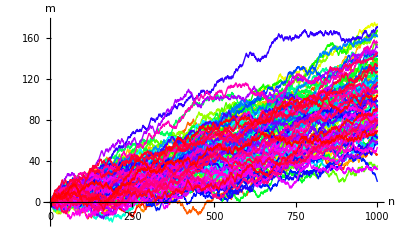

```mathematica
(* parameters *)

nmax=1000; (* max steps *)
z=100; (* number of organisms *)

l=0.45; (* prob step left *)

Do[
m[i,0]=0;
,{i,1,z}]

Do[
Do[
If[Random[Real,{0,1}]<l,m[i,n]=m[i,n-1]-1,m[i,n]=m[i,n-1]+1];
,{i,1,z}];
,{n,1,nmax}];

Do[
plot[i]=ListPlot[Table[{n,m[i,n]},{n,0,nmax}],Joined->True,PlotStyle->Hue[i/z],AxesLabel->{"n","m"}];
,{i,1,z}];

Show[Table[plot[i],{i,1,z}],PlotRange->All]
```

```mathematica
(* the following code will plot the density of organisms (bins) and the expected density, normal distribution solution to diffusion equation (line) *)

If[l==0.5,
mmax=Ceiling[Max[Abs[Max[Flatten[Table[m[i,n],{i,1,z},{n,0,nmax}]]]],Abs[Min[Flatten[Table[m[i,n],{i,1,z},{n,0,nmax}]]]]]/10]*10+5;
mmin=-mmax;,
mmax=Ceiling[Max[Flatten[Table[m[i,n],{i,1,z},{n,0,nmax}]]]/10]*10+5;
mmin=Floor[Min[Flatten[Table[m[i,n],{i,1,z},{n,0,nmax}]]]/10]*10-5;
];

ϵ=0.0001;
d=1/2;

Animate[
hgram=Histogram[Table[m[i,n],{i,1,z}],{10},PlotRange->{{-100,200},All}];
dplot=Plot[10*z/(2*Sqrt[π*d*(n+ϵ)])*E^(-(x-(1-2*l)*n)^2/(4*d*(n+ϵ))),{x,-100,200},PlotRange->All,PlotStyle->Thickness[0.005]];

Show[hgram,dplot,PlotRange->{{-100,200},All},AxesOrigin->{-100,0},PlotLabel->n]

,{n,0,nmax,10},AnimationRunning->False]
```

## Fisher's Equation, Travelling Wave

Here we use Fisher's equation (diffusion + logistic growth) to investigate the spread of a population into new habitat.  We solve the equation for -10 < x < 50, with initial conditions n(x,0)=1 for x<0 and =0 for x>0.

### Using the formula from class,calculate the travelling wave speed (c) for these three sets of parameters: 1) r=1, d=1; 2) r=2, d=1; 3) r=0, d=1 (just diffusion). (1.5 pts)

### Numerically solve for these parameter sets. (Cut out all but last graphic in each to turn in). Is there a constant speed travelling wave in each case? How long does it take for the population to reach x=50? Can a species spread quickly by diffusion alone? (5.5 pts)

No, a species can not spread quickly through diffusion alone as seen in the last graph.

```mathematica
Clear[n]
```

```mathematica
tmax=25; (* how long to run simulation *)
l=50; (* habitat length *)
r=1; (* growth rate *)
d=1; (* diffusion coefficient *)

sol=NDSolve[{
D[n[x,t], t]==d*D[n[x,t], x,x]+r*n[x,t]*(1-n[x,t]),n[x,0]==If[x<0,1,0],Derivative[1,0][n][-10,t]==0,Derivative[1,0][n][l,t]==0},n,{x,-10,l},{t,0,tmax},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid", "MaxPoints"->1000,"MinPoints"->100}}];

Animate[
Plot[Evaluate[n[x,t]/.sol],{x,-10,l},PlotRange->{0,1},PlotLabel->t,PlotStyle->RGBColor[0,1,0],AxesLabel->{"x","n"}]
,{t,0,tmax,tmax/50.},AnimationRunning->False]
```

NDSolve::mxsst: Using maximum number of grid points 1000 allowed by the MaxPoints or MinStepSize options for independent variable x.

```mathematica
tmax=25; (* how long to run simulation *)
l=50; (* habitat length *)
r=2; (* growth rate *)
d=1; (* diffusion coefficient *)

sol=NDSolve[{
D[n[x,t], t]==d*D[n[x,t], x,x]+r*n[x,t]*(1-n[x,t]),n[x,0]==If[x<0,1,0],Derivative[1,0][n][-10,t]==0,Derivative[1,0][n][l,t]==0},n,{x,-10,l},{t,0,tmax},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid", "MaxPoints"->1000,"MinPoints"->100}}];

Animate[
Plot[Evaluate[n[x,t]/.sol],{x,-10,l},PlotRange->{0,1},PlotLabel->t,PlotStyle->RGBColor[0,1,0],AxesLabel->{"x","n"}]
,{t,0,tmax,tmax/50.},AnimationRunning->False]
```

NDSolve::mxsst: Using maximum number of grid points 1000 allowed by the MaxPoints or MinStepSize options for independent variable x.

```mathematica
tmax=25; (* how long to run simulation *)
l=50; (* habitat length *)
r=0; (* growth rate *)
d=1; (* diffusion coefficient *)

sol=NDSolve[{
D[n[x,t], t]==d*D[n[x,t], x,x]+r*n[x,t]*(1-n[x,t]),n[x,0]==If[x<0,1,0],Derivative[1,0][n][-10,t]==0,Derivative[1,0][n][l,t]==0},n,{x,-10,l},{t,0,tmax},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid", "MaxPoints"->1000,"MinPoints"->100}}];

Animate[
Plot[Evaluate[n[x,t]/.sol],{x,-10,l},PlotRange->{0,1},PlotLabel->t,PlotStyle->RGBColor[0,1,0],AxesLabel->{"x","n"}]
,{t,0,tmax,tmax/50.},AnimationRunning->False]
```

NDSolve::mxsst: Using maximum number of grid points 1000 allowed by the MaxPoints or MinStepSize options for independent variable x.

## Fisher's Equation, Critical Patch Size

Again, Fisher's equation, but now we look at a finite domain with hostile exterior.  0 < x < l, with n(0,t)=0 amd n(l,t)=0.

### Let r=2, d=1. Calculate the critical patch size (l_c) using formula from class. (2 pts)

### Using these parameters, numerically solve the model for l<l_c, l>l_c, and l>>l_c until equilibrium is reached. Compare the spatial distribution of organisms in these three cases. (4 pts)

```mathematica
l=5;
tmax=20;
r=2;
d=1;

sol=NDSolve[{
D[n[x,t], t]==d*D[n[x,t], x,x]+r*n[x,t]*(1-n[x,t]),n[x,0]==0.1*x*(1-x/l),n[0,t]==0,n[l,t]==0},n,{x,0,l},{t,0,tmax}];

Animate[
Plot[Evaluate[n[x,t]/.sol],{x,0,l},PlotRange->{-0.01,1},PlotStyle->RGBColor[0,1,0],PlotLabel->t,AxesLabel->{"x","n"}]
,{t,0,tmax,tmax/20.},AnimationRunning->False]
```